```mathematica
lithium1=Transpose[Import["D:\\Partition functions\\Li I.tsv"]][[3;;4]];
lithium2=Transpose[Import["D:\\Partition functions\\Li II.tsv"]][[3;;4]];
lithium3=Transpose[Import["D:\\Partition functions\\Li III.tsv"]][[3;;4]];

sodium1=Transpose[Import["D:\\Partition functions\\Na I.tsv"]][[3;;4]]; 
sodium2=Transpose[Import["D:\\Partition functions\\Na II.tsv"]][[3;;4]];
{{sodium3=Transpose[Import["D:\\Partition functions\\Na III.tsv"]][[3;;4]];}, {□}}

potassium1=Transpose[Import["D:\\Partition functions\\K I.tsv"]][[3;;4]];
potassium2=Transpose[Import["D:\\Partition functions\\K II.tsv"]][[3;;4]];
potassium3=Transpose[Import["D:\\Partition functions\\K III.tsv"]][[3;;4]];

magnesium1=Transpose[Import["D:\\Partition functions\\Mg I.tsv"]][[3;;4]];
magnesium2=Transpose[Import["D:\\Partition functions\\Mg II.tsv"]][[3;;4]];
magnesium3=Transpose[Import["D:\\Partition functions\\Mg III.tsv"]][[3;;4]];

calcium1=Transpose[Import["D:\\Partition functions\\Ca I.tsv"]][[3;;4]];
calcium2=Transpose[Import["D:\\Partition functions\\Ca II.tsv"]][[3;;4]];
calcium3=Transpose[Import["D:\\Partition functions\\Ca III.tsv"]][[3;;4]];

aluminium1=Transpose[Import["D:\\Partition functions\\Al I.tsv"]][[3;;4]];
aluminium2=Transpose[Import["D:\\Partition functions\\Al II.tsv"]][[3;;4]];
aluminium3=Transpose[Import["D:\\Partition functions\\Al III.tsv"]][[3;;4]];

manganese1=Transpose[Import["D:\\Partition functions\\Mn I.tsv"]][[3;;4]];
manganese2=Transpose[Import["D:\\Partition functions\\Mn II.tsv"]][[3;;4]];
manganese3=Transpose[Import["D:\\Partition functions\\Mn III.tsv"]][[3;;4]];

iron1=Transpose[Import["D:\\Partition functions\\Fe I.tsv"]][[3;;4]];
iron2=Transpose[Import["D:\\Partition functions\\Fe II.tsv"]][[3;;4]];
iron3=Transpose[Import["D:\\Partition functions\\Fe III.tsv"]][[3;;4]];

phosphorus1=Transpose[Import["D:\\Partition functions\\P I.tsv"]][[3;;4]];
phosphorus2=Transpose[Import["D:\\Partition functions\\P II.tsv"]][[3;;4]];
phosphorus3=Transpose[Import["D:\\Partition functions\\P III.tsv"]][[3;;4]];

H1=Transpose[Import["D:\\Partition functions\\H I.tsv"]][[3;;4]];
H2=Transpose[Import["D:\\Partition functions\\H II.tsv"]][[3;;4]];
H3=Transpose[Import["D:\\Partition functions\\H III.tsv"]][[3;;4]];

strontium1=Transpose[Import["D:\\Partition functions\\Sr I.tsv"]][[3;;4]];
strontium2=Transpose[Import["D:\\Partition functions\\Sr II.tsv"]][[3;;4]];
strontium3=Transpose[Import["D:\\Partition functions\\Sr III.tsv"]][[3;;4]];

silicon1=Transpose[Import["D:\\Partition functions\\Si I.tsv"]][[3;;4]];
silicon2=Transpose[Import["D:\\Partition functions\\Si II.tsv"]][[3;;4]];
silicon3=Transpose[Import["D:\\Partition functions\\Si III.tsv"]][[3;;4]];

Partfunc[file_,T_]:=Module[{g,levels},g=Rest[file[[1]]]; levels=Rest[file[[2]]]; Total[g*Exp[-levels/(T/11604)]]];
EionLi1=5.391714761; EionLi2=75.6400964;
EionNa1=5.1390769; EionNa2=47.28636;
EionK1=4.34066354; EionK2=31.625;
EionMg1=7.646236; EionMg2=15.035271;
EionCa1=6.1131552; EionCa2=11.871719;
EionAl1=5.985769;EionAl2=18.82855;
EionFe1=7.9024681; EionFe2=16.19921;
EionMn1=7.4340380; EionMn2=15.63999;
EionP1=10.486686; EionP2=19.76949;
EionH1=13.598434599702; EionH2=0;
EionSr1=5.69486745; EionSr2=11.0302765;
EionSi1=8.15168; EionSi2=16.34585;
```

{{Null},{□}}

```mathematica
ne=0.5*10^16; T=5000; L=Sqrt[((6.626*10^-34)^2)/(2*Pi*T*(9.1094*10^-31)*1.38*10^-23)];

(*One-stage ionization quotient: file2 refers to species with higher ionization*)
alpha[file1_,file2_,Eion_,T_,ne_]:=Module[{L},
L=Sqrt[((6.626*10^-34)^2)/(2*Pi*T*(9.1094*10^-31)*1.38*10^-23)];
(2/L^3)*(Partfunc[file2,T]/Partfunc[file1,T])*(10^-6/ne)*Exp[(-Eion/(T/11604))]];

(*Neutral atom quotient (two stages of ionization taken into account)*)
ntlquot[file1_,file2_,file3_,Eion1_,Eion2_,T_,ne_]:=Module[{L,alpha1,alpha2},
L=Sqrt[((6.626*10^-34)^2)/(2*Pi*T*(9.1094*10^-31)*1.38*10^-23)];
alpha1=(2/L^3)*(Partfunc[file2,T]/Partfunc[file1,T])*(10^-6/ne)*Exp[(-Eion1/(T/11604))];
alpha2=(2/L^3)*(Partfunc[file3,T]/Partfunc[file2,T])*(10^-6/ne)*Exp[(-Eion2/(T/11604))];
If[Eion2==0,alpha2=0];
1/(1+alpha1+alpha1*alpha2)];

ion1quot[file1_,file2_,file3_,Eion1_,Eion2_,T_,ne_]:=Module[{L,alpha1,alpha2},
L=Sqrt[((6.626*10^-34)^2)/(2*Pi*T*(9.1094*10^-31)*1.38*10^-23)];
alpha1=(2/L^3)*(Partfunc[file2,T]/Partfunc[file1,T])*(10^-6/ne)*Exp[(-Eion1/(T/11604))];
alpha2=(2/L^3)*(Partfunc[file3,T]/Partfunc[file2,T])*(10^-6/ne)*Exp[(-Eion2/(T/11604))];
If[Eion2==0,alpha2=0];
alpha1/(1+alpha1+alpha1*alpha2)];

Q[stage_,filepartfunc_,Ex_,file1_,file2_,file3_,Eion1_,Eion2_,T_,ne_]:=Module[{output},

If[stage==1,
output=Partfunc[filepartfunc,T]*Exp[Ex/(T/11604)]/ntlquot[file1,file2,file3,Eion1,Eion2,T,ne]];
If[stage==2,
output=Partfunc[filepartfunc,T]*Exp[Ex/(T/11604)]/ion1quot[file1,file2,file3,Eion1,Eion2,T,ne]];
If[stage>2,
output="no data"]; output
	];
```

```mathematica
1.0543676334704525*^-9
```

1.05437×10^-9

```mathematica
RootApproximant[1.0543676334704525*^-9]
```

(-474217895+√224882612477099615)/538868590

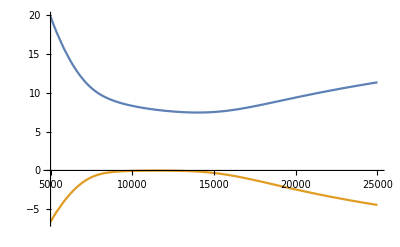

```mathematica
Plot[{Log[Q[2,manganese2,4.81,manganese1,manganese2,manganese3,EionMn1,EionMn2,x,5*10^16]],Log[ion1quot[manganese1,manganese2,manganese3,EionMn1,EionMn2,x,5*10^16]]},{x,5000,25000}]
```